```mathematica
DSolve[-y''[x]+x*y[x]==ϵ*y[x],y[x],x]
```

{{y[x]→AiryAi[x-ϵ] C[1]+AiryBi[x-ϵ] C[2]}}

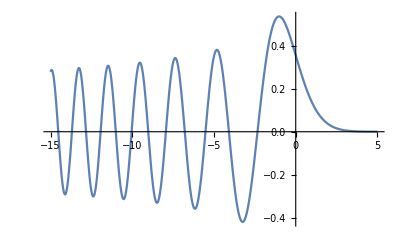

```mathematica
Plot[AiryAi[x],{x,-15,5}]
```

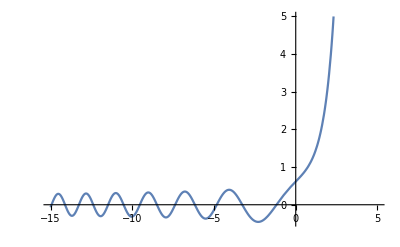

```mathematica
Plot[AiryBi[x],{x,-15,5}]
```

```mathematica
FindRoot[AiryAi[x],{x,-2}]
```

```mathematica
{x->-2.338107410459767}
```

```mathematica
FindRoot[AiryAi[x],{x,-13}]
```

```mathematica
{x->-12.828776752865757}
```

```mathematica
NIntegrate[(AiryAi[x])^2,{x,-2.338107410459767,∞}]
```

```mathematica
0.4916966179009774
```

```mathematica
NIntegrate[(AiryAi[x])^2,{x,-12.828776752865757,∞}]
```

```mathematica
1.1401837256117164
```

```mathematica
Pone[x_]:=(0.4916966179009774)^(-1/2)*AiryAi[x-2.338107410459767]
```

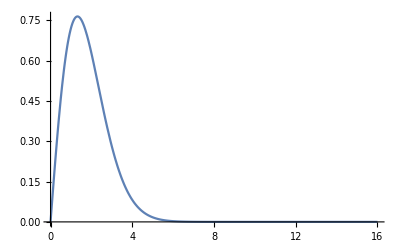

```mathematica
Plot[Pone[x],{x,0,16}]
```

```mathematica
Pten[x_]:=(1.1401837256117164)^(-1/2)*AiryAi[x-12.828776752865757]
```

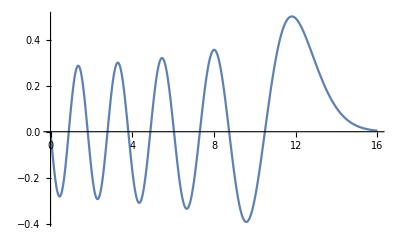

```mathematica
Plot[Pten[x],{x,0,16}]
```

```mathematica
NIntegrate[Pone[x]*Pten[x],{x,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.72352}. NIntegrate obtained -8.86877×10^-17 and 1.56187×10^-16 for the integral and error estimates.

-8.86877×10^-17

```mathematica
NIntegrate[x*(Pone[x])^2,{x,0,∞}]
```

```mathematica
1.558738273638599
```

```mathematica
NIntegrate[x^2*(Pone[x])^2,{x,0,∞}]
```

```mathematica
2.9155980068599967
```

```mathematica
√(2.9155980068599967-(1.558738273638599)^2)
```

```mathematica
0.6970889478066314
```

```mathematica
NIntegrate[x*(Pten[x])^2,{x,0,∞}]
```

```mathematica
8.552517834822023
```

```mathematica
NIntegrate[x^2*(Pten[x])^2,{x,0,∞}]
```

```mathematica
87.77467357595424
```

```mathematica
√(87.77467357595424-(8.552517834822023)^2)
```

```mathematica
3.8248022512288737
```

```mathematica
NIntegrate[-ⅈ Pone[x](Pone'[x]),{x,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.2858}. NIntegrate obtained 0.+1.64799×10^-17 ⅈ and 8.08563×10^-17 for the integral and error estimates.

0.+1.64799×10^-17 ⅈ

```mathematica
NIntegrate[- Pone[x](Pone''[x]),{x,0,∞}]
```

```mathematica
0.7793691368188985
```

```mathematica
√0.7793691368188985
```

```mathematica
0.8828188584409027
```

```mathematica
NIntegrate[-ⅈ Pten[x](Pten'[x]),{x,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {11.8025}. NIntegrate obtained 0.+1.14058×10^-16 ⅈ and 6.10073×10^-14 for the integral and error estimates.

0.+1.14058×10^-16 ⅈ

```mathematica
NIntegrate[-Pten[x](Pten''[x]),{x,0,∞}]
```

```mathematica
4.276258918045443
```

```mathematica
√4.276258918045443
```

```mathematica
2.067911728784728
```

```mathematica
0.6970889478066314*0.8828188584409027
```

0.615403

```mathematica
3.8248022512288737*2.067911728784728
```

7.90935

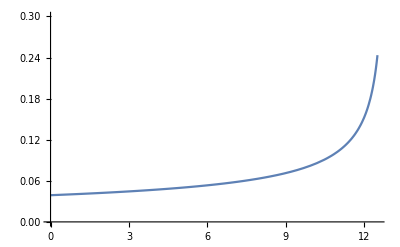

```mathematica
P1=Plot[(4*12.828776752865757*(12.828776752865757-x))^(-1/2),{x,0,12.5},PlotRange->{0,.3}]
```

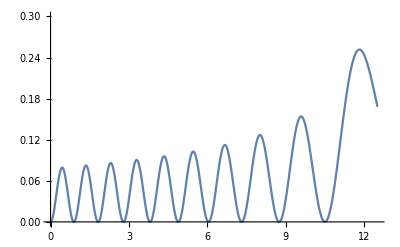

```mathematica
P2=Plot[(Pten[x])^2,{x,0,12.5},PlotRange->{0,.3}]
```

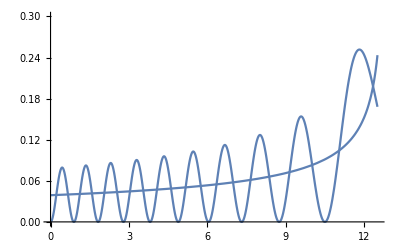

```mathematica
Show[P1,P2]
```